## Quintessence solver

João Victor Silva Rebouças, August 2021
I made this to compare with CAMB and fixed points, so I’m interested in non-dimensional quantities (wϕ, Ωϕ) both today (a=1) and in the far future (a >> 1).
This program solves the background equations for an universe with matter, radiation and quintessence as dark energy.
I use units in which c = 8πG = H_0 = 1
Quintessence has an exponential potential V(ϕ) = V_0 * exp(λϕ)

```mathematica
Clear["Global`*"]
```

## 1. Exponential Potential

### Constants and parameters:

```mathematica
λ = 1; (* Quintessence exponential potential parameter *)
V0 = 10; (* Energy scale *)
ρcr = 3; (* Subscript[ρ, cr] = 3*Subscript[H, 0]^2/(8πG), but Subscript[H, 0] = 8πG = 1 *)
Ωm0 = 0.3; (* Matter fractional abundance today *)
Ωr0 = 5*10^(-5); (* Radiation fractional abundance today *)
```

### Functions of Interest:

```mathematica
V[ϕ_] := V0*Exp[-λ*ϕ];(* I'm using natural units c = Mpl = Subscript[H, 0] = 1 *)
ρϕ[ϕ_, ϕdot_] := V[ϕ] + ϕdot^2/2; (* ϕdot = dϕ/dt *)
ρm[a_]:=ρcr*Ωm0*a^(-3); (* Matter background energy density *)
ρr[a_]:=ρcr*Ωr0*a^(-4); (* Radiation background energy density *)
H[a_,ϕ_,ϕdot_] := Sqrt[Ωr0*a^(-4) + Ωm0*a^(-3) + ρϕ[ϕ, ϕdot]/ρcr] (* Hubble factor from Friedmann equation *)
```

### Equations and Initial Conditions:

```mathematica
scalarfieldeq = ϕ''[t] + 3*H[a[t], ϕ[t], ϕ'[t]]*ϕ'[t] + V'[ϕ[t]]== 0;
friedmanneq = a'[t]== a[t]*H[a[t], ϕ[t], ϕ'[t]];
ϕinitial = 1;
astart = 10^(-7);
tend = 2000;
initialconditions = {ϕ[0] == ϕinitial, ϕ'[0]==0, a[0]==astart};
```

### Solving Numerically:

There are two tricky parts here. The first is to figure out the end limit for the time integration. I want to integrate at least until a=1. The age of the universe (until a=1) should be of order of the Hubble time H_0^(-1) = 1. The second is that NDSolve won’t work with a(0)=0 as initial condition. I chose astart = 10^(-7) which CAMB uses.

```mathematica
λ = 1; (* Quintessence exponential potential parameter *)
V0 = 1;
ρcr = 3; (* Subscript[ρ, cr] = 3*Subscript[H, 0]^2/(8πG), but Subscript[H, 0] = 8πG = 1 *)
Ωm0 = 0.3; (* Matter fractional abundance today *)
Ωr0 = 5*10^(-5); (* Radiation fractional abundance today *)
V[ϕ_] := V0*Exp[-λ*ϕ];(* I'm using natural units c = Mpl = Subscript[H, 0] = 1 *)
ρϕ[ϕ_, ϕdot_] := V[ϕ] + ϕdot^2/2; (* ϕdot = dϕ/dt *)
ρm[a_]:=ρcr*Ωm0*a^(-3); (* Matter background energy density *)
ρr[a_]:=ρcr*Ωr0*a^(-4); (* Radiation background energy density *)
H[a_,ϕ_,ϕdot_] := Sqrt[Ωr0*a^(-4) + Ωm0*a^(-3) + ρϕ[ϕ, ϕdot]/ρcr] (* Hubble factor from Friedmann equation *)
scalarfieldeq = ϕ''[t] + 3*H[a[t], ϕ[t], ϕ'[t]]*ϕ'[t] + V'[ϕ[t]]== 0;
friedmanneq = a'[t]== a[t]*H[a[t], ϕ[t], ϕ'[t]];
ϕinitial = 1; (* Initial condition for the field *)
astart = 10^(-7); (* CAMB uses this astart *)
tend = 2000; (* Arbitrary. I want to integrate at least until convergence to the fixed point *)
(* Remember that Subscript[H, 0]=1 so for cosmologies close to ΛCDM, we should hit a=1 close to t=1 *)
initialconditions = {ϕ[0] == ϕinitial, ϕ'[0]==0, a[0]==astart};
solution = NDSolve[{scalarfieldeq, friedmanneq, initialconditions}, {a, ϕ}, {t, 0, tend}]
asolved[t_]:=First[a[t]/.solution] (* Passing numerical interpolations to functions *)
phisolved[t_]:=First[ϕ[t]/.solution]
```

{{a→InterpolatingFunction[{{0., 2000.}}, <>],ϕ→InterpolatingFunction[{{0., 2000.}}, <>]}}

```mathematica
tofaNotWorking = InverseFunction[asolved[#]&]; (*Not evaluating before a = 0.1 - see note below*)
```

```mathematica
tofa[a_]:=FindRoot[asolved[t]==a,{t,0,tend}][[1]][[2]] (* Technical Note: whenever inverting interpolating functions, one should note that those may not be invertible! If InverseFunction doesn't work, use FindRoot, which relies on root-finding algorithms instead of inverting the function, so you can restrict the domain *)
```

```mathematica
Ωr[a_]:=ρr[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωm[a_]:=ρm[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωϕ[a_]:=ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
wϕ[a_]:=(phisolved'[tofa[a]]^2/2 - V[phisolved[tofa[a]]])/ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]
```

```mathematica
(* Technical Note: since phisolved is a function originally in t, phisolved' = dphi/dt, evaluated at tofa[a]. This prime doesn't use the chain rule, so phi'[f[t]] = dphi/dt evaluated at f[t]. You can check this by running the lines:
  In[1]:= f[t_]:= Sin[t]
 In[2]:= f'[t^2]
Out[2]= Cos[t^2]
 *)
```

### Case Study 1 - λ = 1 (quintessence-dominated):

Following Amendola’s book ‘Dark Energy - Theory and Observations’, section 7.2, for quintessence with an exponential potential and λ < 3(1+w_m), the system goes to the stable node c) where Ωϕ tends to 1 and wϕ tends to -1 + λ.b2/3. For λ = 1 and matter-dominated regime, the system should converge to w = -2/3, Ω = 1. Let’s confirm this:

```mathematica
λ = 1; (* Quintessence exponential potential parameter *)
V0 = 1;
ρcr = 3; (* Subscript[ρ, cr] = 3*Subscript[H, 0]^2/(8πG), but Subscript[H, 0] = 8πG = 1 *)
Ωm0 = 0.3; (* Matter fractional abundance today divided by rhocr *)
Ωr0 = 8.7 * 10^(-5); (* Radiation fractional abundance today *)
V[ϕ_] := V0*Exp[-λ*ϕ];(* I'm using natural units c = Mpl = Subscript[H, 0] = 1 *)
ρϕ[ϕ_, ϕdot_] := V[ϕ] + ϕdot^2/2; (* ϕdot = dϕ/dt *)
ρm[a_]:=ρcr*Ωm0*a^(-3); (* Matter background energy density *)
ρr[a_]:=ρcr*Ωr0*a^(-4); (* Radiation background energy density *)
H[a_,ϕ_,ϕdot_] := Sqrt[Ωr0*a^(-4) + Ωm0*a^(-3) + ρϕ[ϕ, ϕdot]/ρcr] (* Hubble factor from Friedmann equation *)
scalarfieldeq = ϕ''[t] + 3*H[a[t], ϕ[t], ϕ'[t]]*ϕ'[t] + V'[ϕ[t]]== 0;
friedmanneq = a'[t]== a[t]*H[a[t], ϕ[t], ϕ'[t]];
ϕinitial = 1;
astart = 10^(-7);
tend = 2000;
initialconditions = {ϕ[0] == ϕinitial, ϕ'[0]==0, a[0]==astart};
solution = NDSolve[{scalarfieldeq, friedmanneq, initialconditions}, {a, ϕ}, {t, 0, tend}]
asolved[t_]:=First[a[t]/.solution] (* Passing numerical interpolations to functions *)
phisolved[t_]:=First[ϕ[t]/.solution]
tofa[a_]:=FindRoot[asolved[t]==a,{t,0,tend}][[1]][[2]]
Ωr[a_]:=ρr[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωm[a_]:=ρm[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωϕ[a_]:=ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
wϕ[a_]:=(phisolved'[tofa[a]]^2/2 - V[phisolved[tofa[a]]])/ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]
```

{{a→InterpolatingFunction[{{0., 2000.}}, <>],ϕ→InterpolatingFunction[{{0., 2000.}}, <>]}}

Now some plots:

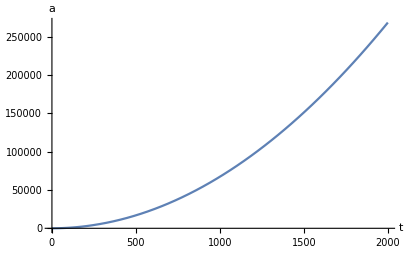

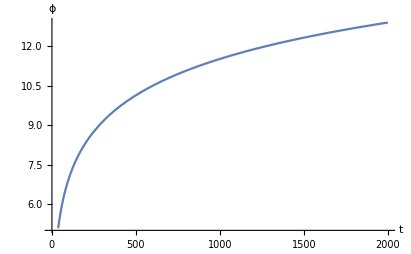

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

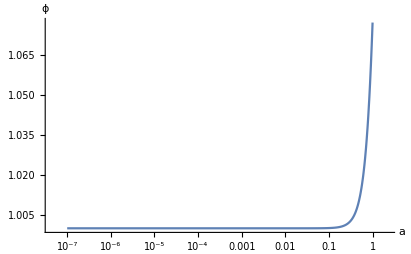

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

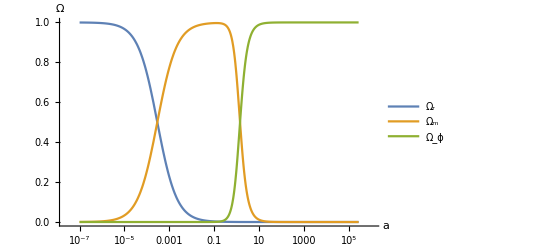

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

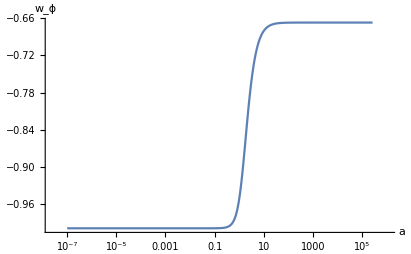

```mathematica
Plot[asolved[t],{t,0,tend}, AxesLabel->{t, a}, LabelStyle->Directive[Bold, Medium]]
Plot[phisolved[t],{t,0,tend}, AxesLabel->{t, ϕ}, LabelStyle->Directive[Bold, Medium]]
LogLinearPlot[phisolved[tofa[a]],{a, astart, 1}, PlotRange->All, AxesLabel->{a, ϕ}, LabelStyle->Directive[Bold, Medium]]
LogLinearPlot[{Ωr[a], Ωm[a], Ωϕ[a]}, {a,astart,asolved[tend]}, AxesLabel->{a, Ω}, LabelStyle->Directive[Bold, Medium], PlotLegends->{"Ω_r","Ω_m","Ω_ϕ"}]
LogLinearPlot[wϕ[a],{a,astart,asolved[tend]}, PlotRange->All, AxesLabel->{a, Subscript[w, ϕ]}, LabelStyle->Directive[Bold, Medium]]
```

And now some raw numbers

```mathematica
Ωϕ[1]
Ωϕ[asolved[tend]]
wϕ[1]
wϕ[asolved[tend]]
```

0.279252

1.

-0.952758

-0.666666

Matches what we expect from fixed points!

### Comparing λ = 1 with CAMB

```mathematica
data = Import["/home/joaov/ReferencesAndCalculations/Joao_mathematica/quintessence/exponentialpotentiallmbd1.dat", "Table"]//ToExpression;
phis = Transpose[data][[2]];
as = Transpose[data][[1]];
omegas = Transpose[data][[4]];
tablephis=Table[{as[[i]],phis[[i]]},{i,1,8832}];
tableomegas = Table[{as[[i]],omegas[[i]]},{i,1,8832}];
comparisonphis = Table[{as[[i]], ( phis[[i]] - phisolved[tofa[as[[i]]]] )/phisolved[tofa[ as[[i]]] ]}, {i,1, 8832}];
comparisonomegas = Table[{as[[i]], (omegas[[i]] - Ωϕ[as[[i]]])/Ωϕ[ as[[i]] ]}, {i,1, 8832}];
```

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

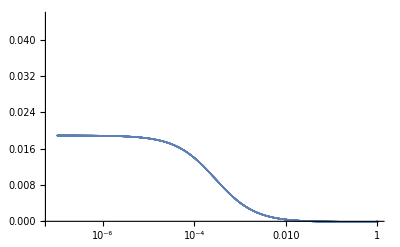

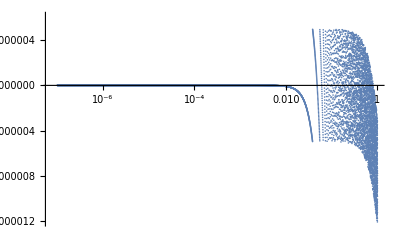

```mathematica
ListLogLinearPlot[comparisonomegas]
ListLogLinearPlot[comparisonphis]
```

### Case Study 2: λ = sqrt(5) (tracking)

From Amendola’s book, for λ.b2 > 3, the system tends to fixed point d), a stable spiral with Ωϕ = 3(1+w_m)/λ^2 and wϕ = w_m. This means we should get Ω_ϕ = 0.6 and w_ϕ = 0 as an asymptotic limit. Let’s confirm that

```mathematica
λ = Sqrt[5]; (* Quintessence exponential potential parameter *)
V0 = 1;
ρcr = 3; (* Subscript[ρ, cr] = 3*Subscript[H, 0]^2/(8πG), but Subscript[H, 0] = 8πG = 1 *)
Ωm0 = 0.3; (* Matter fractional abundance today divided by rhocr *)
Ωr0 = 8.7 * 10^(-5); (* Radiation fractional abundance today *)
V[ϕ_] := V0*Exp[-λ*ϕ];(* I'm using natural units c = Mpl = Subscript[H, 0] = 1 *)
ρϕ[ϕ_, ϕdot_] := V[ϕ] + ϕdot^2/2; (* ϕdot = dϕ/dt *)
ρm[a_]:=ρcr*Ωm0*a^(-3); (* Matter background energy density *)
ρr[a_]:=ρcr*Ωr0*a^(-4); (* Radiation background energy density *)
H[a_,ϕ_,ϕdot_] := Sqrt[Ωr0*a^(-4) + Ωm0*a^(-3) + ρϕ[ϕ, ϕdot]/ρcr] (* Hubble factor from Friedmann equation *)
scalarfieldeq = ϕ''[t] + 3*H[a[t], ϕ[t], ϕ'[t]]*ϕ'[t] + V'[ϕ[t]]== 0;
friedmanneq = a'[t]== a[t]*H[a[t], ϕ[t], ϕ'[t]];
ϕinitial = 1;
astart = 10^(-7);
tend = 2000;
initialconditions = {ϕ[0] == ϕinitial, ϕ'[0]==0, a[0]==astart};
solution = NDSolve[{scalarfieldeq, friedmanneq, initialconditions}, {a, ϕ}, {t, 0, tend}]
asolved[t_]:=First[a[t]/.solution] (* Passing numerical interpolations to functions *)
phisolved[t_]:=First[ϕ[t]/.solution]
tofa[a_]:=FindRoot[asolved[t]==a,{t,0,tend}][[1]][[2]]
Ωr[a_]:=ρr[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωm[a_]:=ρm[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωϕ[a_]:=ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
wϕ[a_]:=(phisolved'[tofa[a]]^2/2 - V[phisolved[tofa[a]]])/ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]
```

{{a→InterpolatingFunction[{{0., 2000.}}, <>],ϕ→InterpolatingFunction[{{0., 2000.}}, <>]}}

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

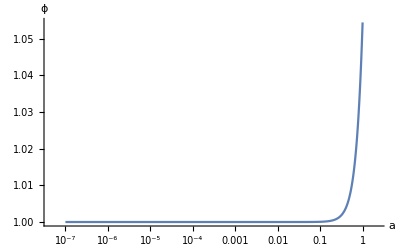

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

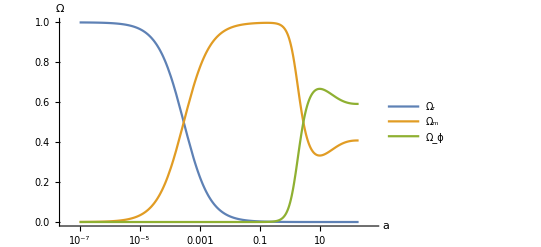

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

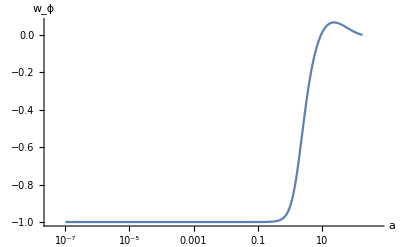

```mathematica
LogLinearPlot[phisolved[tofa[a]],{a, astart, 1}, PlotRange->All, AxesLabel->{a, ϕ}, LabelStyle->Directive[Bold, Medium]]
LogLinearPlot[{Ωr[a], Ωm[a], Ωϕ[a]}, {a,astart,asolved[tend]}, AxesLabel->{a, Ω}, LabelStyle->Directive[Bold, Medium], PlotLegends->{"Ω_r","Ω_m","Ω_ϕ"}]
LogLinearPlot[wϕ[a],{a,astart,asolved[tend]}, PlotRange->All, AxesLabel->{a, Subscript[w, ϕ]}, LabelStyle->Directive[Bold, Medium]]
```

```mathematica
Ωϕ[1]
Ωϕ[asolved[tend]]
wϕ[1]
wϕ[asolved[tend]]
```

0.0985623

0.591659

-0.922753

-0.00191443

Again, matching what we expect from the fixed points

### Comparing λ = sqrt(5) with CAMB

```mathematica
data = Import["/home/joaov/ReferencesAndCalculations/Joao_mathematica/quintessence/exponentialpotentiallmbdsqrt5.dat", "Table"]//ToExpression;
phis = Transpose[data][[2]];
as = Transpose[data][[1]];
omegas = Transpose[data][[4]];
tablephis=Table[{as[[i]],phis[[i]]},{i,1,8832}];
tableomegas = Table[{as[[i]],omegas[[i]]},{i,1,8832}];
comparisonphis = Table[{as[[i]], ( phis[[i]] - phisolved[tofa[as[[i]]]] )/phisolved[tofa[ as[[i]]] ]}, {i,1, 8832}];
comparisonomegas = Table[{as[[i]], (omegas[[i]] - Ωϕ[as[[i]]])/Ωϕ[ as[[i]] ]}, {i,1, 8832}];
```

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

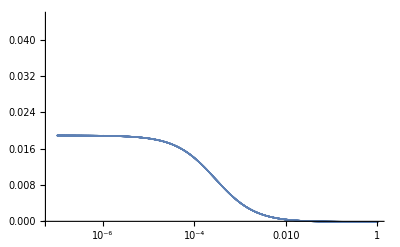

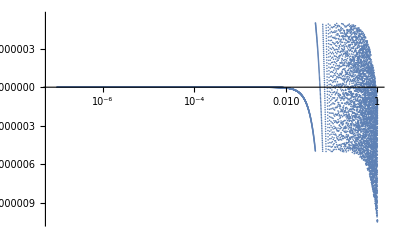

```mathematica
ListLogLinearPlot[comparisonomegas]
ListLogLinearPlot[comparisonphis] (* The early difference in the Ω plot is due to Omega_r mismatch *)
```

CAMB and Mathematica have a fractional difference of at most 10^(-5)

```mathematica
data = Import["/home/joaov/ReferencesAndCalculations/Joao_mathematica/quintessence/exponentialpotentiallmbd1.dat", "Table"]//ToExpression;
phis = Transpose[data][[2]];
as = Transpose[data][[1]];
omegas = Transpose[data][[4]];
tablephis=Table[{as[[i]],phis[[i]]},{i,1,8832}];
tableomegas = Table[{as[[i]],omegas[[i]]},{i,1,8832}];
comparisonphis = Table[{as[[i]], ( phis[[i]] - phisolved[tofa[as[[i]]]] )/phisolved[tofa[ as[[i]]] ]}, {i,1, 8832}];
comparisonomegas = Table[{as[[i]], (omegas[[i]] - Ωϕ[as[[i]]])/Ωϕ[ as[[i]] ]}, {i,1, 8832}];
```

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

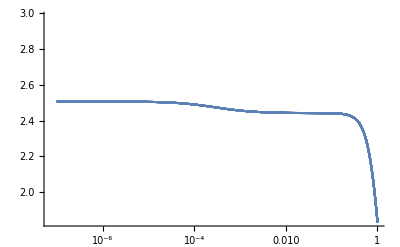

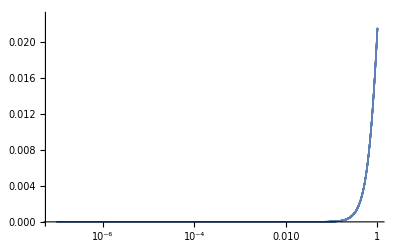

```mathematica
ListLogLinearPlot[comparisonomegas]
ListLogLinearPlot[comparisonphis]
```

## 2. Hyperbolic Cosine

Now I want to compare my results with https://arxiv.org/pdf/1810.08586.pdf

### Test 1: β = 6

```mathematica
β = 6; (* Quintessence potential parameter *)
V0 = 2.2;
V[ϕ_] := V0*Cosh[β*ϕ];(* I'm using natural units c = Mpl = Subscript[H, 0] = 1 *)
ρϕ[ϕ_, ϕdot_] := V[ϕ] + ϕdot^2/2; (* ϕdot = dϕ/dt *)
H[a_,ϕ_,ϕdot_] := Sqrt[Ωr0*a^(-4) + Ωm0*a^(-3) + ρϕ[ϕ, ϕdot]/ρcr] (* Hubble factor from Friedmann equation *)
scalarfieldeq = ϕ''[t] + 3*H[a[t], ϕ[t], ϕ'[t]]*ϕ'[t] + V'[ϕ[t]]== 0;
friedmanneq = a'[t]== a[t]*H[a[t], ϕ[t], ϕ'[t]];
ϕinitial = 0.7;
astart = 10^(-7);
tend = 2000;
initialconditions = {ϕ[0] == ϕinitial, ϕ'[0]==0, a[0]==astart};
solution = NDSolve[{scalarfieldeq, friedmanneq, initialconditions}, {a, ϕ}, {t, 0, tend}]
asolved[t_]:=First[a[t]/.solution] (* Passing numerical interpolations to functions *)
phisolved[t_]:=First[ϕ[t]/.solution]
tofa[a_]:=FindRoot[asolved[t]==a,{t,0,tend}][[1]][[2]]
Ωr[a_]:=ρr[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωm[a_]:=ρm[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωϕ[a_]:=ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
wϕ[a_]:=(phisolved'[tofa[a]]^2/2 - V[phisolved[tofa[a]]])/ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]
```

{{a→InterpolatingFunction[{{0., 2000.}}, <>],ϕ→InterpolatingFunction[{{0., 2000.}}, <>]}}

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

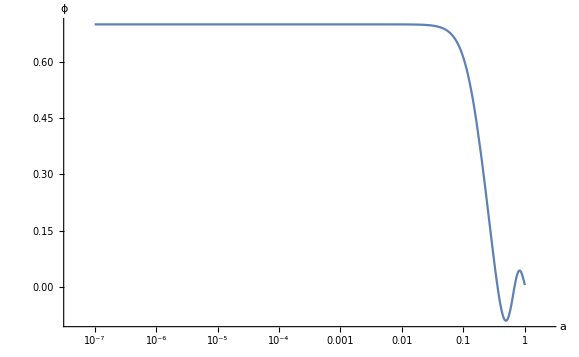

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

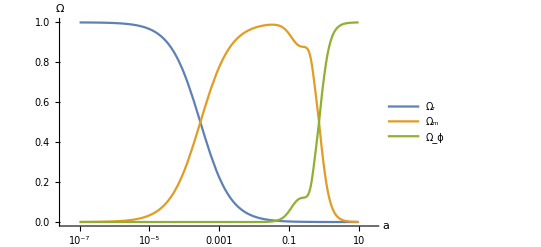

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

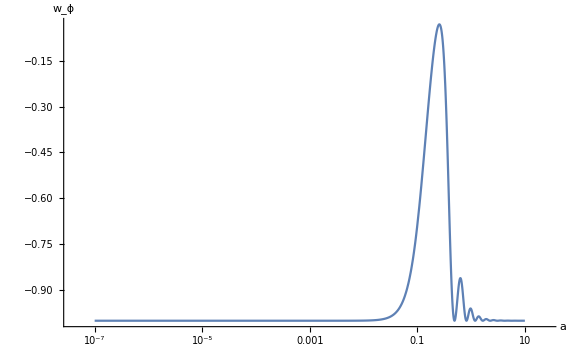

```mathematica
LogLinearPlot[phisolved[tofa[a]],{a, astart, 1}, PlotRange->All, AxesLabel->{a, ϕ}, LabelStyle->Directive[Bold, Medium]]
LogLinearPlot[{Ωr[a], Ωm[a], Ωϕ[a]}, {a,astart,10}, AxesLabel->{a, Ω}, LabelStyle->Directive[Bold, Medium], PlotLegends->{"Ω_r","Ω_m","Ω_ϕ"}]
plotw6=LogLinearPlot[wϕ[a],{a,astart,10}, PlotRange->All, AxesLabel->{a, Subscript[w, ϕ]}, LabelStyle->Directive[Bold, Medium]] (* This is taking some minutes *)
```

```mathematica
Ωϕ[1]
wϕ[1]
```

0.713691

-0.961653

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

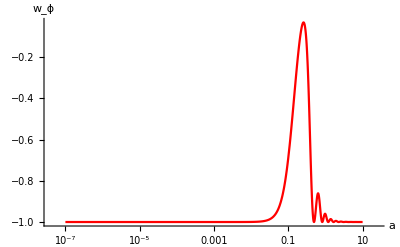

```mathematica
plotw6 = LogLinearPlot[wϕ[a],{a,astart,10}, PlotRange->All, AxesLabel->{a, Subscript[w, ϕ]}, LabelStyle->Directive[Bold, Medium], PlotStyle->Red];
```

### Comparing β = 6 with CAMB

```mathematica
data = Import["/home/joaov/ReferencesAndCalculations/Joao_mathematica/quintessence/test_cosh_bg.dat", "Table"]//ToExpression;
```

```mathematica
comparisonphis = Table[{as[[i]], ( phis[[i]] - phisolved[tofa[as[[i]]]] )/phisolved[tofa[ as[[i]]] ]}, {i,8000, 8831}]; (*Taking too long!!*)
```

```mathematica
data = Import["/home/joaov/ReferencesAndCalculations/Joao_mathematica/quintessence/test_cosh_bg.dat", "Table"]//ToExpression;
phis = Transpose[data][[2]];
as = Transpose[data][[1]];
omegas = Transpose[data][[4]];
tablephis=Table[{as[[i]],phis[[i]]},{i,1,8831}];
tableomegas = Table[{as[[i]],omegas[[i]]},{i,1,8831}];
comparisonphis = Table[{as[[i]], ( phis[[i]] - phisolved[tofa[as[[i]]]] )/phisolved[tofa[ as[[i]]] ]}, {i,8000, 8831}];
comparisonomegas = Table[{as[[i]], (omegas[[i]] - Ωϕ[as[[i]]])/Ωϕ[ as[[i]] ]}, {i,8000, 8831}];
```

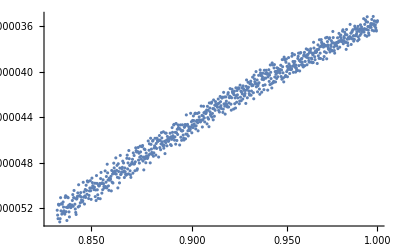

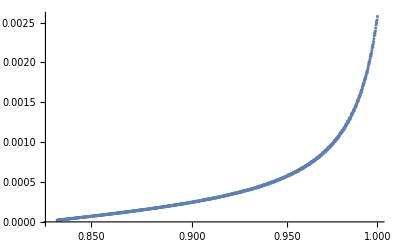

```mathematica
ListLogLinearPlot[comparisonomegas]
ListLogLinearPlot[comparisonphis]
```

### Test 2: β = 8

{{a→InterpolatingFunction[{{0., 2000.}}, <>],ϕ→InterpolatingFunction[{{0., 2000.}}, <>]}}

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

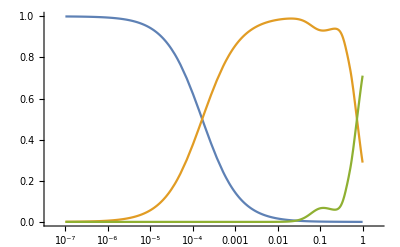

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

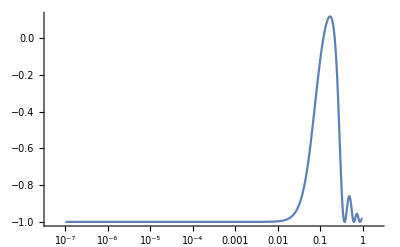

```mathematica
β = 8; (* Quintessence potential parameter *)
V0 = 2.2;
V[ϕ_] := V0*Cosh[β*ϕ];(* I'm using natural units c = Mpl = Subscript[H, 0] = 1 *)
ρϕ[ϕ_, ϕdot_] := V[ϕ] + ϕdot^2/2; (* ϕdot = dϕ/dt *)
H[a_,ϕ_,ϕdot_] := Sqrt[Ωr0*a^(-4) + Ωm0*a^(-3) + ρϕ[ϕ, ϕdot]/ρcr] (* Hubble factor from Friedmann equation *)
scalarfieldeq = ϕ''[t] + 3*H[a[t], ϕ[t], ϕ'[t]]*ϕ'[t] + V'[ϕ[t]]== 0;
friedmanneq = a'[t]== a[t]*H[a[t], ϕ[t], ϕ'[t]];
ϕinitial = 0.7;
astart = 10^(-7);
tend = 2000;
initialconditions = {ϕ[0] == ϕinitial, ϕ'[0]==0, a[0]==astart};
solution = NDSolve[{scalarfieldeq, friedmanneq, initialconditions}, {a, ϕ}, {t, 0, tend}]
asolved[t_]:=First[a[t]/.solution] (* Passing numerical interpolations to functions *)
phisolved[t_]:=First[ϕ[t]/.solution]
tofa[a_]:=FindRoot[asolved[t]==a,{t,0,tend}][[1]][[2]]
Ωr[a_]:=ρr[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωm[a_]:=ρm[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωϕ[a_]:=ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
wϕ[a_]:=(phisolved'[tofa[a]]^2/2 - V[phisolved[tofa[a]]])/ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]
LogLinearPlot[{Ωr[a],Ωm[a], Ωϕ[a]}, {a,astart,1}, PlotRange->All]
p8 = LogLinearPlot[wϕ[a], {a, astart, 1}, PlotRange->All]
```

### Test 3: β = 10

{{a→InterpolatingFunction[{{0., 2000.}}, <>],ϕ→InterpolatingFunction[{{0., 2000.}}, <>]}}

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

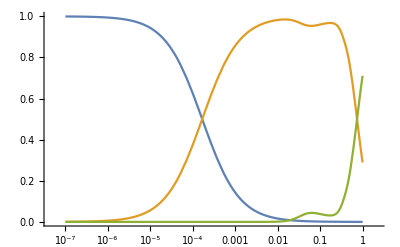

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

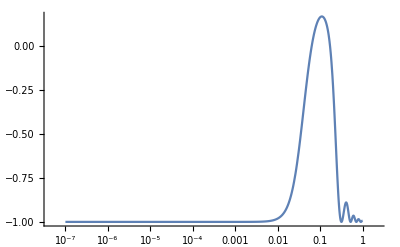

```mathematica
β = 10; (* Quintessence potential parameter *)
V0 = 2.2;
V[ϕ_] := V0*Cosh[β*ϕ];(* I'm using natural units c = Mpl = Subscript[H, 0] = 1 *)
ρϕ[ϕ_, ϕdot_] := V[ϕ] + ϕdot^2/2; (* ϕdot = dϕ/dt *)
H[a_,ϕ_,ϕdot_] := Sqrt[Ωr0*a^(-4) + Ωm0*a^(-3) + ρϕ[ϕ, ϕdot]/ρcr] (* Hubble factor from Friedmann equation *)
scalarfieldeq = ϕ''[t] + 3*H[a[t], ϕ[t], ϕ'[t]]*ϕ'[t] + V'[ϕ[t]]== 0;
friedmanneq = a'[t]== a[t]*H[a[t], ϕ[t], ϕ'[t]];
ϕinitial = 0.7;
astart = 10^(-7);
tend = 2000;
initialconditions = {ϕ[0] == ϕinitial, ϕ'[0]==0, a[0]==astart};
solution = NDSolve[{scalarfieldeq, friedmanneq, initialconditions}, {a, ϕ}, {t, 0, tend}]
asolved[t_]:=First[a[t]/.solution] (* Passing numerical interpolations to functions *)
phisolved[t_]:=First[ϕ[t]/.solution]
tofa[a_]:=FindRoot[asolved[t]==a,{t,0,tend}][[1]][[2]]
Ωr[a_]:=ρr[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωm[a_]:=ρm[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωϕ[a_]:=ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
wϕ[a_]:=(phisolved'[tofa[a]]^2/2 - V[phisolved[tofa[a]]])/ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]
LogLinearPlot[{Ωr[a],Ωm[a], Ωϕ[a]}, {a,astart,1}, PlotRange->All]
p10 = LogLinearPlot[wϕ[a], {a, astart, 1}, PlotRange->All]
```

```mathematica
(* Everything seems to be matching both CAMB and the article *)
```

```mathematica
Show[p6, p8, p10]
```

-Graphics-

## 3. Hyperbolic Secant

```mathematica
α = 3.5; (* Quintessence exponential potential parameter *)
ϵ = 1;
V0 = 1.1;
V[ϕ_] := V0*(1+ϵ*Sech[α*ϕ]);(* I'm using natural units c = Mpl = Subscript[H, 0] = 1 *)
ρϕ[ϕ_, ϕdot_] := V[ϕ] + ϕdot^2/2; (* ϕdot = dϕ/dt *)
ρm[a_]:=ρcr*Ωm0*a^(-3); (* Matter background energy density *)
ρr[a_]:=ρcr*Ωr0*a^(-4); (* Radiation background energy density *)
H[a_,ϕ_,ϕdot_] := Sqrt[Ωr0*a^(-4) + Ωm0*a^(-3) + ρϕ[ϕ, ϕdot]/ρcr] (* Hubble factor from Friedmann equation *)
scalarfieldeq = ϕ''[t] + 3*H[a[t], ϕ[t], ϕ'[t]]*ϕ'[t] + V'[ϕ[t]]== 0;
friedmanneq = a'[t]== a[t]*H[a[t], ϕ[t], ϕ'[t]];
ϕinitial = 0.7;
astart = 10^(-7);
tend = 2000;
initialconditions = {ϕ[0] == ϕinitial, ϕ'[0]==0, a[0]==astart};
solution = NDSolve[{scalarfieldeq, friedmanneq, initialconditions}, {a, ϕ}, {t, 0, tend}]
asolved[t_]:=First[a[t]/.solution] (* Passing numerical interpolations to functions *)
phisolved[t_]:=First[ϕ[t]/.solution]
tofa[a_]:=FindRoot[asolved[t]==a,{t,0,tend}][[1]][[2]]
Ωr[a_]:=ρr[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωm[a_]:=ρm[a]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
Ωϕ[a_]:=ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]/(ρr[a]+ρm[a]+ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]])
wϕ[a_]:=(phisolved'[tofa[a]]^2/2 - V[phisolved[tofa[a]]])/ρϕ[phisolved[tofa[a]], phisolved'[tofa[a]]]
```

{{a→InterpolatingFunction[{{0., 2000.}}, <>],ϕ→InterpolatingFunction[{{0., 2000.}}, <>]}}

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

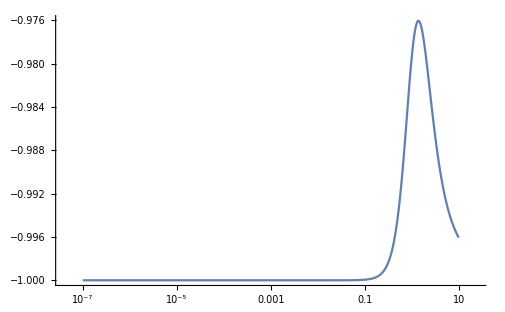

FindRoot::nlnum: The function value {1.×10^-7-1. a} is not a list of numbers with dimensions {1} at {t} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

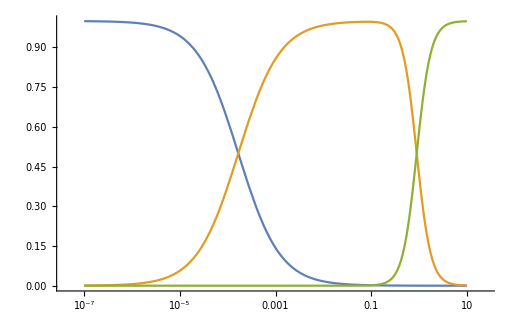

```mathematica
LogLinearPlot[wϕ[a],{a,astart,10}, PlotRange->All]
LogLinearPlot[{Ωr[a], Ωm[a], Ωϕ[a]}, {a,astart,10}]
```

## (Outdated) Take 2: Dynamical System Approach

### Equations and Solution

```mathematica
lmbd = 100;
lnastart = -12;
```

```mathematica
eqx1 = x1'[lna] == -3x1[lna] + Sqrt[6]*lmbd*x2[lna]^2/2 + x1[lna](3 + 3x1[lna]^2-3x2[lna]^2+x3[lna]^2)/2;
eqx2 = x2'[lna]==-Sqrt[6]*lmbd*x1[lna]*x2[lna] /2+x2[lna](3 + 3x1[lna]^2-3x2[lna]^2+x3[lna]^2)/2;
eqx3 = x3'[lna]==-2x3[lna] + x3[lna](3 + 3x1[lna]^2-3x2[lna]^2+x3[lna]^2)/2;
dynamicalsystem = {eqx1, eqx2, eqx3};
```

```mathematica
initialconditions = {x1[lnastart]==1*10^(-8), x2[lnastart]==1*10^(-6), x3[lnastart]==0.9999};
```

```mathematica
solution = NDSolve[{dynamicalsystem, initialconditions}, {x1, x2, x3}, {lna, lnastart, 0}]
```

{{x1→InterpolatingFunction[{{-12., 0.}}, <>],x2→InterpolatingFunction[{{-12., 0.}}, <>],x3→InterpolatingFunction[{{-12., 0.}}, <>]}}

### Plotting

```mathematica
w[lna_]:=(x1[lna]^2 - x2[lna]^2)/(x1[lna]^2 + x2[lna]^2)/.solution
Subscript[Ω, q][lna_] := x1[lna]^2 + x2[lna]^2/.solution
Subscript[Ω, r][lna_]:=x3[lna]^2/.solution
Subscript[Ω, m][lna_]:=1 - Subscript[Ω, q][lna] - Subscript[Ω, r][lna]
```

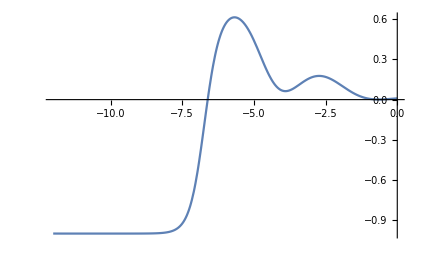

```mathematica
Plot[w[lna], {lna, lnastart, 0}, PlotRange->All]
```

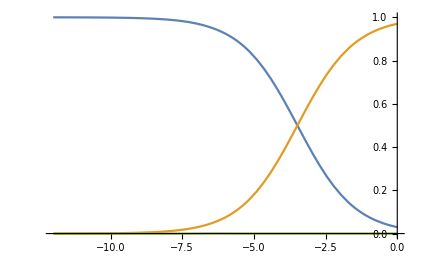

```mathematica
Plot[{Subscript[Ω, r][lna], Subscript[Ω, m][lna], Subscript[Ω, q][lna]}, {lna, lnastart,0}]
```

The only question remaining: